## max_weight=100; 2; 50; 100

```mathematica
data1BB={{10,0.0003245},{20,0.0007823},{30,0.0014351},{40,0.0001709},{60,0.0010683},{80,0.000591},{100,0.0003613},{120,0.0004815},{140,0.0007967},{160,0.003165},{180,0.0077749},{200,0.0395338},{240,0.0598471},{280,0.0744865},{320,0.0005687},{360,0.0069811},{400,0.0545084}};

data1DP={{10,0.0002744},{20,0.0002457},{30,0.0005454},{40,0.0005183},{60,0.0006983},{80,0.0014383},{100,0.0014406},{120,0.0021292},{140,0.001108},{160,0.0011106},{180,0.0013149},{200,0.0012922},{240,0.0016137},{280,0.0017341},{320,0.0024917},{360,0.0043101},{400,0.0035035}};
```

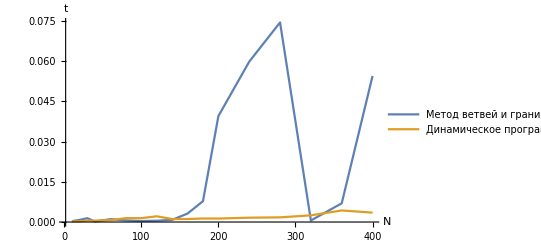

```mathematica
p1=ListLinePlot[{data1BB,data1DP},PlotLegends->{"Метод ветвей и границ","Динамическое программирование"},AxesLabel->{N,t},PlotRange->All]
```

## max_weight=1000; 10; 50; 100

```mathematica
data2BB={{100,0.2525562},{150,1.00128},{200,0.0998694},{250,0.0285265},{300,0.0289044},{350,0.4910161},{400,1.508146},{450,0.5413149},{500,0.1018274}};

data2DP={{100,0.0069784},{150,0.0170074},{200,0.0291616},{250,0.0275469},{300,0.0572715},{350,0.0499883},{400,0.0331244},{450,0.0638715},{500,0.0818246}};
```

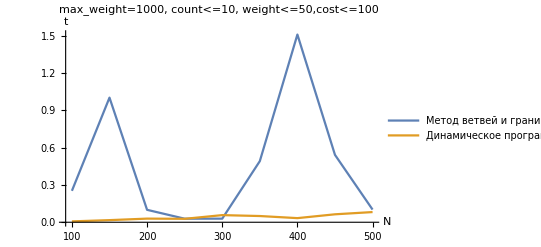

```mathematica
p2=ListLinePlot[{data2BB,data2DP},PlotLegends->{"Метод ветвей и границ","Динамическое программирование"},AxesLabel->{N,t},PlotRange->All,PlotLabel->Style[Framed["max_weight=1000, count<=10, weight<=50,cost<=100"],14,Blue,Background->Lighter[Yellow]]]
```

## max_weight=3000; 10; 50; 100

```mathematica
data2BB={{3,0.0000922},{10,0.0002198},{20,0.0003273},{30,0.0009635},{40,0.0013412},{50,0.0046299},{60,0.2031471},{80,0.4062406},{100,8.174172}};

data2DP={{3,0.0019239},{10,0.0049425},{20,0.0155247},{30,0.0227736},{40,0.0269569},{50,0.0186903},{60,0.0168929},{80,0.0233439},{100,0.0451468}};
```

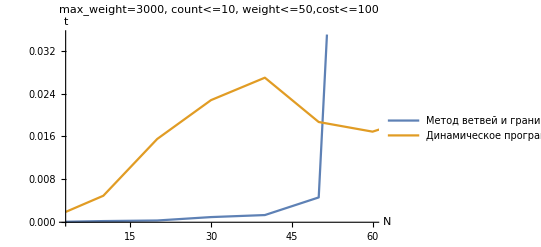

```mathematica
p3=ListLinePlot[{data2BB,data2DP},PlotLegends->{"Метод ветвей и границ","Динамическое программирование"},AxesLabel->{N,t},PlotRange->{{3,60},{0,0.035}},PlotLabel->Style[Framed["max_weight=3000, count<=10, weight<=50,cost<=100"],14,Blue,Background->Lighter[Yellow]]]
```

## max_weight=5000; 10; 50; 100

```mathematica
data3BB={{3,0.0000615},{10,0.0003079},{20,0.0002928},{30,0.0006659},{40,0.0011723},{50,0.0021845},{60,0.0250904},{70,0.1227945},{80,0.0622976},{90,0.0390126},{100,0.0432035},{120,4.788448},{140,249.0449}};

data3DP={{3,0.0017708},{10,0.014632},{20,0.0095022},{30,0.0241106},{40,0.0451049},{50,0.0508481},{60,0.0672566},{70,0.0565453},{80,0.063984},{90,0.0850002},{100,0.0855044},{120,0.0809421},{140,0.1001592}};
```

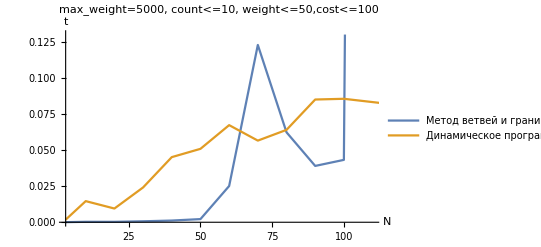

```mathematica
p4=ListLinePlot[{data3BB,data3DP},PlotLegends->{"Метод ветвей и границ","Динамическое программирование"},AxesLabel->{N,t},PlotRange->{{3,110},{0,0.13}},PlotLabel->Style[Framed["max_weight=5000, count<=10, weight<=50,cost<=100"],14,Blue,Background->Lighter[Yellow]]]
```